```mathematica
Remove["Global`*"];
fd=((2/L)*(1-(d/L))); (* PDF of line picking on a line *)
fr =2/(π*Sqrt[Da^2-r^2 ]); (* PDF of line picking on a circle *)
fr*fd;
a={d∈Reals,r∈Reals,w∈Reals,Da∈Reals,L∈Reals,L>Da>w>0,w>r>0, w>d>0 , Da > w , Da > 0};
```

```mathematica
CDF1 = FullSimplify[Integrate[fd*fr, {r, 0, w},{d, 0, Sqrt[w^2 - r^2]}, Assumptions -> a], a]
```

(-Da w √((Da-w) (Da+w))+Da (Da^2-2 w^2) ArcSin[w/Da]+4 Da^2 L EllipticE[w^2/Da^2]+4 L (-Da^2+w^2) EllipticK[w^2/Da^2])/(Da L^2 π)

```mathematica
PDF1=FullSimplify[Dt[CDF1,w,Constants -> {L, Da}],a]
```

(4 w (-Da ArcSin[w/Da]+L EllipticK[w^2/Da^2]))/(Da L^2 π)

```mathematica
(* we need an integration constant for CDF2 and CDF3 this is easiest to get by evaluating CDF1 at Da but the function does not exist there so we take the limit as w -> Da *)
K1[w_] = ((-Da)*w*Sqrt[(Da - w)*(Da + w)] + Da*(Da^2 - 2*w^2)*ArcSin[w/Da] + 
   4*Da^2*L*EllipticE[w^2/Da^2] )/
  (Da*L^2*Pi);
K1 = FullSimplify[K1[Da]] (* our constant works for CDF2 *)
```

-(Da (-8 L+Da π))/(2 L^2 π)

```mathematica
b ={d∈Reals,r∈Reals,w∈Reals,Da∈Reals,L∈Reals,L>Da,w>Da>d >0, w>r>0,w>d>0};

CDF2=FullSimplify[Integrate[fd*fr,{r,0,Da},{d,Sqrt[Da^2-r^2],Sqrt[w^2-r^2]},Assumptions->b] +K1, b]
```

(Da^2 π-2 π w^2+8 L w EllipticE[Da^2/w^2])/(2 L^2 π)

```mathematica
PDF2=FullSimplify[Dt[CDF2,w,Constants -> {L, Da}],b]
```

(-2 π w+4 L EllipticK[Da^2/w^2])/(L^2 π)

```mathematica
c = {d∈Reals,r∈Reals,w∈Reals,Da∈Reals,L∈Reals,w>L>d>Da>r>0,w>Sqrt[w^2-L^2],Da>Sqrt[w^2-L^2],L>0};

CDF3=FullSimplify[CDF2 -Integrate[fd*fr,{r, 0, Sqrt[w^2-L^2]},{d, L, Sqrt[w^2-r^2]},Assumptions->c], c ]
```

1/(2 L^2 π)(Da^2 π-2 π w^2+8 L w EllipticE[Da^2/w^2]-2 (-√((Da^2+L^2-w^2) (-L^2+w^2))+(Da^2-2 (L^2+w^2)) ArcCsc[Da/(√(-L^2+w^2))]+4 L w EllipticE[ArcCsc[Da/(√(-L^2+w^2))],Da^2/w^2]))

```mathematica
PDF3 = FullSimplify[Dt[CDF3, w,Constants -> {L, Da}], c]
```

-(4 (w ArcSec[Da/(√(-L^2+w^2))]+L EllipticF[ArcCsc[Da/(√(-L^2+w^2))],Da^2/w^2]-L EllipticK[Da^2/w^2]))/(L^2 π)

```mathematica
CForm[CDF1]
```

(-(Da*w*Sqrt((Da - w)*(Da + w))) + 
     Da*(Power(Da,2) - 2*Power(w,2))*ArcSin(w/Da) + 
     4*Power(Da,2)*L*EllipticE(Power(w,2)/Power(Da,2)) + 
     4*L*(-Power(Da,2) + Power(w,2))*EllipticK(Power(w,2)/Power(Da,2)))/
   (Da*Power(L,2)*Pi)

```mathematica
CForm[CDF2]
```

(Power(Da,2)*Pi - 2*Pi*Power(w,2) + 8*L*w*EllipticE(Power(Da,2)/Power(w,2)))/
   (2.*Power(L,2)*Pi)

```mathematica
CForm[CDF3]
```

(Power(Da,2)*Pi - 2*Pi*Power(w,2) + 8*L*w*EllipticE(Power(Da,2)/Power(w,2)) - 
     2*(-Sqrt((Power(Da,2) + Power(L,2) - Power(w,2))*
           (-Power(L,2) + Power(w,2))) + 
        (Power(Da,2) - 2*(Power(L,2) + Power(w,2)))*
         ArcCsc(Da/Sqrt(-Power(L,2) + Power(w,2))) + 
        4*L*w*EllipticE(ArcCsc(Da/Sqrt(-Power(L,2) + Power(w,2))),
          Power(Da,2)/Power(w,2))))/(2.*Power(L,2)*Pi)

```mathematica
CForm[PDF1]
```

(4*w*(-(Da*ArcSin(w/Da)) + L*EllipticK(Power(w,2)/Power(Da,2))))/
   (Da*Power(L,2)*Pi)

```mathematica
CForm[PDF2]
```

(-2*Pi*w + 4*L*EllipticK(Power(Da,2)/Power(w,2)))/(Power(L,2)*Pi)

```mathematica
CForm[PDF3]
```

(-4*(w*ArcSec(Da/Sqrt(-Power(L,2) + Power(w,2))) + 
       L*EllipticF(ArcCsc(Da/Sqrt(-Power(L,2) + Power(w,2))),
         Power(Da,2)/Power(w,2)) - L*EllipticK(Power(Da,2)/Power(w,2))))/
   (Power(L,2)*Pi)

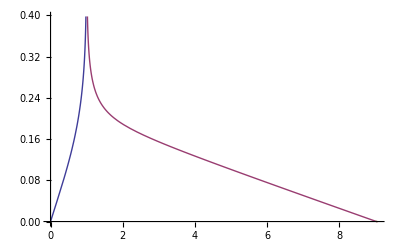

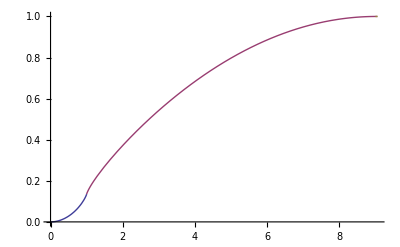

```mathematica
Da=1;
L=9;
Plot[{PDF1,PDF2,PDF3},{w,0,Sqrt[L^2+Da^2]}]
Plot[{CDF1,CDF2,CDF3},{w,0,Sqrt[L^2+Da^2]}]
```